```mathematica
ncsu=Import["C:\\Users\\Gabriel\\Downloads\\ncsu_red_brick_letters.eps"]
```

-Graphics-

```mathematica
?Type
```

Information::notfound: Symbol "Type" not found.

```mathematica
ncsu
```

```mathematica
pointsN=List[{.1,.1},{.1,.2},{.1,.3},{.1,.4},{.1,.5},{.1,.6},{.1,.7},{.1,.8},{.1,.9},{.2,.9},{.245,.8},{.29,.7},{.335,.6},{.38,.5},{.425,.4},{.47,.3},{.515,.2},{.55,.1},{.65,.1},{.65,.2},{.65,.3},{.65,.4},{.65,.5},{.65,.6},{.65,.7},{.65,.8},{.65,.9}];
offsetN[x_]=Table[{x,0},{i,27}];
pointsN1[x_]=(pointsN+offsetN[x])*Table[{4096/5,4096},{i,27}];
```

```mathematica
pointsC={{.55,.7},{.52,.8},{.45,.88},{.35,.9},{.25,.88},{.15,.8},{.12,.7},{.1,.6},{.1,.5},{.1,.4},{.12,.3},{.15,.2},{.25,.12},{.35,.1},{.45,.12},{.52,.2},{.55,.3}};
offsetC[x_]=Table[{x,0},{i,17}];
pointsC1[x_]=(pointsC+offsetC[x])*Table[{4096/5,4096},{i,17}];
```

```mathematica
pointsS={{.1,.3},{.13,.2},{.20,.12},{.32,.1},{.45,.12},{.52,.2},{.55,.3},{.5,.4},{.4,.48},{.25,.52},{.15,.6},{.1,.7},{.13,.8},{.20,.88},{.32,.9},{.45,.88},{.52,.8},{.55,.7}};
offsetS[x_]=Table[{x,0},{i,18}];
pointsS1[x_]=(pointsS+offsetS[x])*Table[{4096/5,4096},{i,18}];
```

```mathematica
pointsT={{.1,.9},{.2,.9},{.3,.9},{.4,.9},{.5,.9},{.6,.9},{.35,.9},{.35,.8},{.35,.7},{.35,.6},{.35,.5},{.35,.4},{.35,.3},{.35,.2},{.35,.1}};
offsetT[x_]=Table[{x,0},{i,15}];
pointsT1[x_]=(pointsT+offsetT[x])*Table[{4096/5,4096},{i,15}];
```

```mathematica
pointsA={{.1,.1},{.1375,.2},{.1750,.3},{.2125,.4},{.25,.5},{.2875,.6},{.325,.7},{.3625,.8},{.4,.9},{.5,.9},{.5375,.8},{.575,.7},{.6125,.6},{.65,.5},{.6875,.4},{.725,.3},{.7625,.2},{.8,.1},{.615,.33},{.505,.33},{.395,.33},{.285,.33}};
offsetA[x_]=Table[{x,0},{i,22}];
pointsA1[x_]=(pointsA+offsetA[x])*Table[{4096/5,4096},{i,22}];
```

```mathematica
pointsE={{.5,.1},{.4,.1},{.3,.1},{.2,.1},{.1,.1},{.1,.2},{.1,.3},{.1,.4},{.1,.5},{.22,.55},{.33,.55},{.45,.55},{.1,.6},{.1,.7},{.1,.8},{.1,.9},{.2,.9},{.3,.9},{.4,.9},{.5,.9},{.1,.9}};
offsetE[x_]=Table[{x,0},{i,21}];
pointsE1[x_]=(pointsE+offsetE[x])*Table[{4096/5,4096},{i,21}];
```

```mathematica
ReturnPath= (Table[{i,.1},{i,.82,.02,-.033}]*Table[{4096,4096},{i,25}])
```

{{3358.72,409.6},{3223.55,409.6},{3088.38,409.6},{2953.22,409.6},{2818.05,409.6},{2682.88,409.6},{2547.71,409.6},{2412.54,409.6},{2277.38,409.6},{2142.21,409.6},{2007.04,409.6},{1871.87,409.6},{1736.7,409.6},{1601.54,409.6},{1466.37,409.6},{1331.2,409.6},{1196.03,409.6},{1060.86,409.6},{925.696,409.6},{790.528,409.6},{655.36,409.6},{520.192,409.6},{385.024,409.6},{249.856,409.6},{114.688,409.6}}

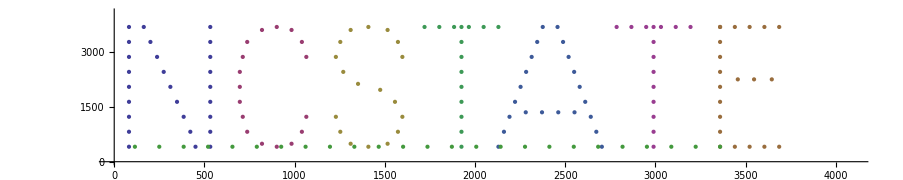

```mathematica
pointers = ListPlot[{pointsN1[0],pointsC1[.75],pointsS1[1.4],pointsT1[2],pointsA1[2.5],pointsT1[3.3],pointsE1[4],ReturnPath},PlotRange->{{0,4096},{0,4096}},AspectRatio->1/5,Joined->False]
```

```mathematica
pointsN*Table[{1/9,1},{i,15}]
```

Thread::tdlen: Objects of unequal length in {{0.1, 0.1}, {0.1, 0.2}, {0.1, 0.3}, {0.1, 0.4}, {0.1, 0.5}, {0.1, 0.6}, {0.1, 0.7}, {0.1, 0.8}, {0.1, 0.9}, {0.2, 0.9}, {0.245, 0.8}, {0.29, 0.7}, {0.335, 0.6}, {0.38, 0.5}, {0.425, 0.4}, {0.47, 0.3}, {0.515, 0.2}, {0.55, 0.1}, {0.65, 0.1}, {0.65, 0.2}, {0.65, 0.3}, {0.65, 0.4}, {0.65, 0.5}, {0.65, 0.6}, {0.65, 0.7}, {0.65, 0.8}, {0.65, 0.9}}\ {{1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}, {1/9, 1}} cannot be combined.

{{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1},{1/9,1}} {{0.1,0.1},{0.1,0.2},{0.1,0.3},{0.1,0.4},{0.1,0.5},{0.1,0.6},{0.1,0.7},{0.1,0.8},{0.1,0.9},{0.2,0.9},{0.245,0.8},{0.29,0.7},{0.335,0.6},{0.38,0.5},{0.425,0.4},{0.47,0.3},{0.515,0.2},{0.55,0.1},{0.65,0.1},{0.65,0.2},{0.65,0.3},{0.65,0.4},{0.65,0.5},{0.65,0.6},{0.65,0.7},{0.65,0.8},{0.65,0.9}}

```mathematica
Show[{ncsu,ncsu}]
```

-Graphics-

```mathematica
bob=Flatten[{pointsN1[0],pointsC1[.75],pointsS1[1.4],pointsT1[2],pointsA1[2.5],pointsT1[3.3],pointsE1[4],ReturnPath},1]
```

{{81.92,409.6},{81.92,819.2},{81.92,1228.8},{81.92,1638.4},{81.92,2048.},{81.92,2457.6},{81.92,2867.2},{81.92,3276.8},{81.92,3686.4},{163.84,3686.4},{200.704,3276.8},{237.568,2867.2},{274.432,2457.6},{311.296,2048.},{348.16,1638.4},{385.024,1228.8},{421.888,819.2},{450.56,409.6},{532.48,409.6},{532.48,819.2},{532.48,1228.8},{532.48,1638.4},{532.48,2048.},{532.48,2457.6},{532.48,2867.2},{532.48,3276.8},{532.48,3686.4},{1064.96,2867.2},{1040.38,3276.8},{983.04,3604.48},{901.12,3686.4},{819.2,3604.48},{737.28,3276.8},{712.704,2867.2},{696.32,2457.6},{696.32,2048.},{696.32,1638.4},{712.704,1228.8},{737.28,819.2},{819.2,491.52},{901.12,409.6},{983.04,491.52},{1040.38,819.2},{1064.96,1228.8},{1228.8,1228.8},{1253.38,819.2},{1310.72,491.52},{1409.02,409.6},{1515.52,491.52},{1572.86,819.2},{1597.44,1228.8},{1556.48,1638.4},{1474.56,1966.08},{1351.68,2129.92},{1269.76,2457.6},{1228.8,2867.2},{1253.38,3276.8},{1310.72,3604.48},{1409.02,3686.4},{1515.52,3604.48},{1572.86,3276.8},{1597.44,2867.2},{1720.32,3686.4},{1802.24,3686.4},{1884.16,3686.4},{1966.08,3686.4},{2048.,3686.4},{2129.92,3686.4},{1925.12,3686.4},{1925.12,3276.8},{1925.12,2867.2},{1925.12,2457.6},{1925.12,2048.},{1925.12,1638.4},{1925.12,1228.8},{1925.12,819.2},{1925.12,409.6},{2129.92,409.6},{2160.64,819.2},{2191.36,1228.8},{2222.08,1638.4},{2252.8,2048.},{2283.52,2457.6},{2314.24,2867.2},{2344.96,3276.8},{2375.68,3686.4},{2457.6,3686.4},{2488.32,3276.8},{2519.04,2867.2},{2549.76,2457.6},{2580.48,2048.},{2611.2,1638.4},{2641.92,1228.8},{2672.64,819.2},{2703.36,409.6},{2551.81,1351.68},{2461.7,1351.68},{2371.58,1351.68},{2281.47,1351.68},{2785.28,3686.4},{2867.2,3686.4},{2949.12,3686.4},{3031.04,3686.4},{3112.96,3686.4},{3194.88,3686.4},{2990.08,3686.4},{2990.08,3276.8},{2990.08,2867.2},{2990.08,2457.6},{2990.08,2048.},{2990.08,1638.4},{2990.08,1228.8},{2990.08,819.2},{2990.08,409.6},{3686.4,409.6},{3604.48,409.6},{3522.56,409.6},{3440.64,409.6},{3358.72,409.6},{3358.72,819.2},{3358.72,1228.8},{3358.72,1638.4},{3358.72,2048.},{3457.02,2252.8},{3547.14,2252.8},{3645.44,2252.8},{3358.72,2457.6},{3358.72,2867.2},{3358.72,3276.8},{3358.72,3686.4},{3440.64,3686.4},{3522.56,3686.4},{3604.48,3686.4},{3686.4,3686.4},{3358.72,3686.4},{3358.72,409.6},{3223.55,409.6},{3088.38,409.6},{2953.22,409.6},{2818.05,409.6},{2682.88,409.6},{2547.71,409.6},{2412.54,409.6},{2277.38,409.6},{2142.21,409.6},{2007.04,409.6},{1871.87,409.6},{1736.7,409.6},{1601.54,409.6},{1466.37,409.6},{1331.2,409.6},{1196.03,409.6},{1060.86,409.6},{925.696,409.6},{790.528,409.6},{655.36,409.6},{520.192,409.6},{385.024,409.6},{249.856,409.6},{114.688,409.6}}

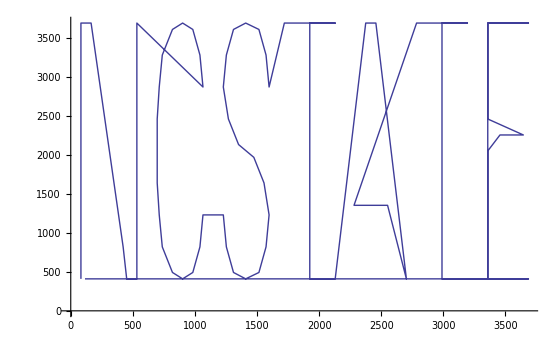

```mathematica
ListPlot[bob,Joined->True]
```